```mathematica
Predicting Silver Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

## Resources

- KAG/USDT hourly price: Recent (≥ 2025) Bitmart data through API.

## In This Notebook

LPPLS model implementation (2026 ed.) for Silver price in USD.
Uses KAG price as a proxy for Silver’s price, due to current lack of access to high quality (hourly) Spot Silver price data.

```mathematica
base=DirectoryName[NotebookFileName[]];
lastPriceDate=DateString[DatePlus[Today, 0],"ISODate"]
```

2026-01-31

```mathematica
hourlyPricesCsv=base<>"./csv/Bitmart_KAG_USDT_1h.csv";
prices =Import[hourlyPricesCsv, HeaderLines->1]
```

```mathematica
(* First price date: *)
firstDownloadedDateTime=prices[[1]][[1]];
{firstDownloadedDate,firstDownloadedTime}=StringSplit[firstDownloadedDateTime];
firstPriceDate=firstDownloadedDate
```

2024-12-31

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[-1]][[1]]
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, 0], "ISODate"]==lastPriceDate, lastDownloadedTime=="23:00:00"}
```

2026-01-31 07:00:00

{2026-01-31,07:00:00}

{True,False}

```mathematica
closingPrices={#[[1]],#[[5]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Convert to seconds *)
hourlyPricesTs={UnixTime[#[[1]]], #[[2]]}&/@closingPricesFilter
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[hourlyPricesTs, First]
```

```mathematica
Length[hourlyPrices]
```

9489

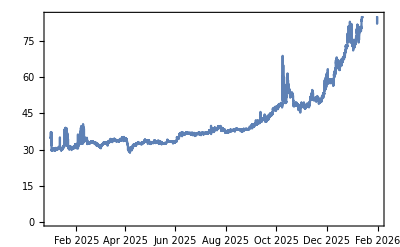

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Silver(KAG)_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/csv/Silver(KAG)_price-hourly-20241231-20260131.csv

```mathematica
{FromUnixTime[hourlyPrices[[1]][[1]]],FromUnixTime[hourlyPrices[[-1]][[1]]]}
```

{Tue 31 Dec 2024 23:00:00GMT+1,Sat 31 Jan 2026 07:00:00GMT+1}

```mathematica
(* Use the Log Price *)
logPrice= {#[[1]], Log[#[[2]]]}&/@hourlyPrices
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2024-01-01", lastPriceDate}, {"2025-01-01", lastPriceDate},{"2025-07-01", "2026-01-28"}(* Pre-crash *)}
```

{{2024-01-01,2026-01-31},{2025-01-01,2026-01-31},{2025-07-01,2026-01-28}}

```mathematica
bubbleN=Length[bubblesDate]
```

3

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1704063600,1769814000},{1735686000,1769814000},{1751324400,1769554800}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{761,395,211}

```mathematica
bubbles=Table[Select[logPrice,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1735682400,3.55241},{1735686000,3.55428},{1751324400,3.58938}}

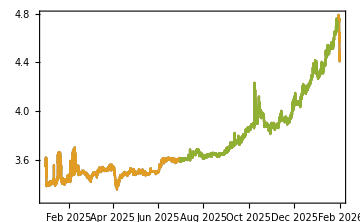

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.0036,0.774575},{1.0036,0.774575},{1.00616,0.982192}}

```mathematica
Length/@bubblesScaled
```

{9482,9481,5065}

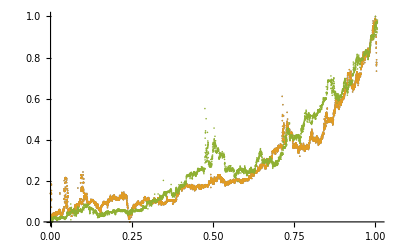

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-Silver-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Silver-1.tsv,/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Silver-2.tsv,/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Silver-3.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.09
```

0.09

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{17.5364,9458.91},{17.5344,9457.91},{17.5819,5041.86}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{5.28065,0.0236291,0.0016968},{5.27232,0.0236117,0.00169555},{2.11279,0.0204728,0.00189035}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

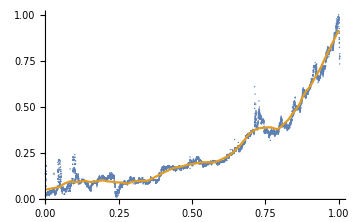
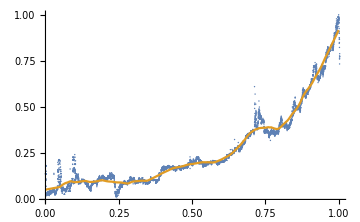
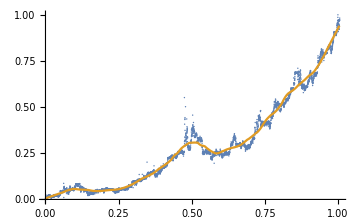

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

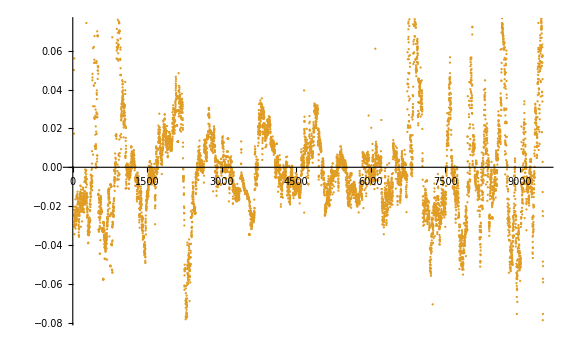
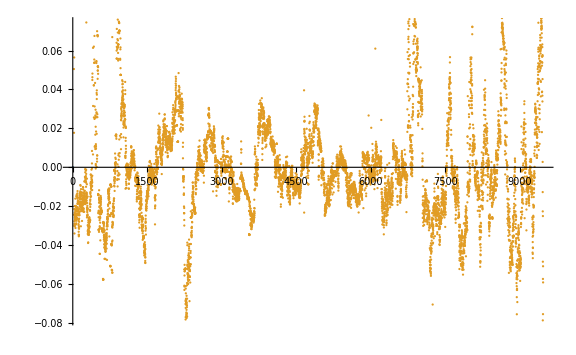
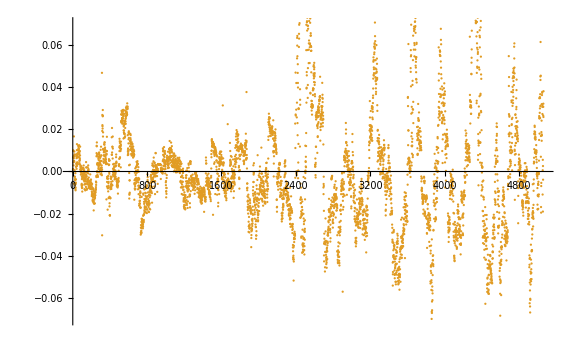

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0272553,0.0272406,0.0253606}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{7.05303,7.04465,3.26058}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{7.05303 > 5.28065,7.04465 > 5.27232,3.26058 > 2.11279}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.0272986,0.0272838,0.0254163}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0272986 > 0.0236291,0.0272838 > 0.0236117,0.0254163 > 0.0204728}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0236209,0.0236035,0.0204594}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0273066,0.0272918,0.0254303}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0273066 > 0.0236291,0.0272918 > 0.0236117,0.0254303 > 0.0204728}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0236278,0.0236104,0.0204707}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

```mathematica
(* Or, select 2nd bubble for fitting: *)
bubble=2
```

```mathematica
(* Or, select last bubble for fitting: *)
bubble=bubbleN
```

3

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{17.5819,5041.86}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 2 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=2;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.00616

2.29052

```mathematica
(* Define 7 days resolution scaled interval step: *)
stepTc=7/bubblesDays[[bubble]]//N
```

0.0331754

```mathematica
(* Define 10 days resolution scaled initial time step *)
stepTi=10/bubblesDays[[bubble]]//N
```

0.0473934

```mathematica
(* Slow. Shortcut below *)
Now[]
fits=
Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

Fri 30 Jan 2026 16:50:03GMT+1[]

{4852.67,{{a→3.4376,b→-3.40847,c→-0.00309397,d→0.0458192,T_1→0.,tc→1.03943,m→0.1,ω→7.2,RSS→6.66043,ℛerror→0.00131681,ℛσ→0.0362664,LL→15884.4,ρ→0.956876,σ→-0.0105342,μ→-5.8172×10^-17},{a→3.43149,b→-3.40139,c→0.000946809,d→0.0466328,T_1→0.0473934,tc→1.03943,m→0.1,ω→7.3,RSS→6.63645,ℛerror→0.00137714,ℛσ→0.0370868,LL→15031.2,ρ→0.957027,σ→-0.010754,μ→-1.74691×10^-16},{a→3.44655,b→-3.41898,c→-0.00460409,d→0.0460141,T_1→0.0947867,tc→1.03943,m→0.1,ω→7.2,RSS→6.49914,ℛerror→0.00141903,ℛσ→0.0376453,LL→14235.7,ρ→0.957258,σ→-0.0108872,μ→3.71012×10^-17},{a→2.00479,b→-2.0136,c→-0.0438695,d→0.0263463,T_1→0.14218,tc→1.03943,m→0.2,ω→6.4,RSS→5.78886,ℛerror→0.00133322,ℛσ→0.0364881,LL→13406.3,ρ→0.95237,σ→-0.0111256,μ→4.12034×10^-17},{a→2.03425,b→-2.05381,c→-0.0542803,d→0.0247433,T_1→0.189573,tc→1.03943,m→0.2,ω→6.3,RSS→5.22508,ℛerror→0.00127348,ℛσ→0.0356597,LL→12579.5,ρ→0.94785,σ→-0.011364,μ→-8.14307×10^-17},{a→1.0452,b→-1.19184,c→-0.106688,d→-0.0391128,T_1→0.236967,tc→1.00626,m→0.5,ω→4.9,RSS→4.54683,ℛerror→0.00117641,ℛσ→0.0342723,LL→11754.1,ρ→0.94035,σ→-0.0116583,μ→6.6174×10^-18},{a→1.04227,b→-1.18671,c→-0.118643,d→0.0127816,T_1→0.28436,tc→1.00626,m→0.5,ω→5.4,RSS→4.22652,ℛerror→0.00116561,ℛσ→0.0341129,LL→10926.2,ρ→0.936177,σ→-0.01199,μ→3.11478×10^-18},{a→1.04578,b→-1.19607,c→-0.119262,d→0.0305723,T_1→0.331754,tc→1.00626,m→0.5,ω→5.5,RSS→4.12097,ℛerror→0.00121634,ℛσ→0.0348453,LL→10129.2,ρ→0.935911,σ→-0.012272,μ→1.72487×10^-17},{a→0.974807,b→-1.19371,c→-0.151864,d→0.0280458,T_1→0.379147,tc→1.00626,m→0.6,ω→5.4,RSS→4.07927,ℛerror→0.00129542,ℛσ→0.0359577,LL→9347.91,ρ→0.937453,σ→-0.0125153,μ→1.26804×10^-17},{a→1.03379,b→-1.15854,c→-0.106478,d→-0.0735637,T_1→0.42654,tc→1.00626,m→0.5,ω→4.8,RSS→3.82602,ℛerror→0.00131433,ℛσ→0.0362164,LL→8554.09,ρ→0.934181,σ→-0.0129198,μ→1.59545×10^-17},{a→1.0245,b→-1.13106,c→-0.103101,d→-0.0990161,T_1→0.473934,tc→1.00626,m→0.5,ω→4.7,RSS→3.68046,ℛerror→0.00137742,ℛσ→0.037072,LL→7754.6,ρ→0.932341,σ→-0.013402,μ→-2.48455×10^-17},{a→1.04133,b→-1.18238,c→-0.066837,d→-0.0833936,T_1→0.521327,tc→1.00626,m→0.5,ω→4.6,RSS→2.32472,ℛerror→0.000955102,ℛσ→0.0308667,LL→8164.82,ρ→0.959289,σ→-0.00871577,μ→-1.8931×10^-17}}}

```mathematica
(* Shortcut: *)
fits={4852.666755,{{a->3.437597454125617,b->-3.4084696380044632,c->-0.0030939651287513054,d->0.04581922968984257,Subscript[T, 1]->0.,tc->1.0394347037514489,m->0.1,ω->7.2,RSS->6.66043136218688,ℛerror->0.0013168112618004903,ℛσ->0.036266390210271345,LL->15884.42628868,ρ->0.95687605616594,σ->-0.010534219155804315,μ->-5.817197392849749*^-17},{a->3.4314896387688485,b->-3.4013854700574173,c->0.0009468088848551036,d->0.046632804033658624,Subscript[T, 1]->0.04739336492890995,tc->1.0394347037514489,m->0.1,ω->7.3,RSS->6.636453010591358,ℛerror->0.0013771431854308692,ℛσ->0.0370867992117172,LL->15031.180419390825,ρ->0.9570269473209517,σ->-0.010754020470382486,μ->-1.7469095302109066*^-16},{a->3.446552896656118,b->-3.4189775255984096,c->-0.004604093601416409,d->0.04601414659218468,Subscript[T, 1]->0.0947867298578199,tc->1.0394347037514489,m->0.1,ω->7.2,RSS->6.499136636294938,ℛerror->0.0014190254664399429,ℛσ->0.03764530400034571,LL->14235.665916504415,ρ->0.9572575291170946,σ->-0.0108872266002218,μ->3.7101180671724464*^-17},{a->2.0047917121680667,b->-2.013598486201417,c->-0.04386945670671651,d->0.02634632591154197,Subscript[T, 1]->0.14218009478672985,tc->1.0394347037514489,m->0.2,ω->6.4,RSS->5.78886160667274,ℛerror->0.0013332246906201614,ℛσ->0.036488147584361835,LL->13406.300980704804,ρ->0.952370109804489,σ->-0.011125582151603086,μ->4.120344465852068*^-17},{a->2.034248446742898,b->-2.0538147265139894,c->-0.054280337658338895,d->0.024743280797937736,Subscript[T, 1]->0.1895734597156398,tc->1.0394347037514489,m->0.2,ω->6.300000000000001,RSS->5.225076656418205,ℛerror->0.0012734771280570813,ℛσ->0.03565974740397921,LL->12579.519176291353,ρ->0.947850019261624,σ->-0.011363974627188907,μ->-8.143066206686241*^-17},{a->1.045198231145101,b->-1.1918386405927583,c->-0.10668828293332634,d->-0.039112823129551694,Subscript[T, 1]->0.23696682464454974,tc->1.0062593483012119,m->0.5,ω->4.9,RSS->4.546829682669791,ℛerror->0.001176411302113788,ℛσ->0.03427226108372035,LL->11754.081115584635,ρ->0.9403495154444041,σ->-0.011658257409585492,μ->6.617403042701922*^-18},{a->1.0422711176125237,b->-1.1867108201178564,c->-0.11864266751937134,d->0.012781634949481735,Subscript[T, 1]->0.2843601895734597,tc->1.0062593483012119,m->0.5,ω->5.4,RSS->4.226519716102418,ℛerror->0.0011656149244628842,ℛσ->0.0341128912457907,LL->10926.180358686948,ρ->0.936176887296757,σ->-0.011990029650373886,μ->3.1147825239344758*^-18},{a->1.0457778417665633,b->-1.1960702603135802,c->-0.11926225287381473,d->0.030572304155759417,Subscript[T, 1]->0.33175355450236965,tc->1.0062593483012119,m->0.5,ω->5.5,RSS->4.120973689684255,ℛerror->0.001216344064251551,ℛσ->0.03484528347003819,LL->10129.210407129907,ρ->0.9359105639951508,σ->-0.01227201567478129,μ->1.7248714592777398*^-17},{a->0.9748072409652325,b->-1.1937129735290717,c->-0.15186400258044674,d->0.028045768942837897,Subscript[T, 1]->0.3791469194312796,tc->1.0062593483012119,m->0.6,ω->5.4,RSS->4.0792663743972835,ℛerror->0.0012954164415361331,ℛσ->0.035957654151008094,LL->9347.912576501396,ρ->0.937452553721471,σ->-0.012515346119886302,μ->1.268035574103153*^-17},{a->1.033793397895247,b->-1.1585446682579972,c->-0.10647837208054702,d->-0.07356370578207085,Subscript[T, 1]->0.42654028436018954,tc->1.0062593483012119,m->0.5,ω->4.8,RSS->3.826019844532993,ℛerror->0.0013143317913201626,ℛσ->0.036216409706519924,LL->8554.08787830764,ρ->0.9341809413624629,σ->-0.01291978684143061,μ->1.5954537309743083*^-17},{a->1.0244987349539647,b->-1.1310585110041227,c->-0.10310098542155166,d->-0.09901608114888089,Subscript[T, 1]->0.4739336492890995,tc->1.0062593483012119,m->0.5,ω->4.7,RSS->3.6804609433783395,ℛerror->0.0013774180177314145,ℛσ->0.03707198326241917,LL->7754.602138123294,ρ->0.9323406471774758,σ->-0.013402027794795057,μ->-2.4845520082034106*^-17},{a->1.0413301542162678,b->-1.182383728738678,c->-0.0668370299725084,d->-0.08339355035110026,Subscript[T, 1]->0.5213270142180094,tc->1.0062593483012119,m->0.5,ω->4.6,RSS->2.3247181811991253,ℛerror->0.000955101964338178,ℛσ->0.03086670298153761,LL->8164.824800170482,ρ->0.9592891619301305,σ->-0.00871576587982655,μ->-1.8930990346562583*^-17}}};
```

```mathematica
(* Timing in hours: *)
fits[[1]]/60/60
```

1.34796

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→1.03943 | ℛσ→0.0362664 | LL→15884.4
T_1→0.0473934 | tc→1.03943 | ℛσ→0.0370868 | LL→15031.2
T_1→0.0947867 | tc→1.03943 | ℛσ→0.0376453 | LL→14235.7
T_1→0.14218 | tc→1.03943 | ℛσ→0.0364881 | LL→13406.3
T_1→0.189573 | tc→1.03943 | ℛσ→0.0356597 | LL→12579.5
T_1→0.236967 | tc→1.00626 | ℛσ→0.0342723 | LL→11754.1
T_1→0.28436 | tc→1.00626 | ℛσ→0.0341129 | LL→10926.2
T_1→0.331754 | tc→1.00626 | ℛσ→0.0348453 | LL→10129.2
T_1→0.379147 | tc→1.00626 | ℛσ→0.0359577 | LL→9347.91
T_1→0.42654 | tc→1.00626 | ℛσ→0.0362164 | LL→8554.09
T_1→0.473934 | tc→1.00626 | ℛσ→0.037072 | LL→7754.6
T_1→0.521327 | tc→1.00626 | ℛσ→0.0308667 | LL→8164.82

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.02008

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.00626

1.03943

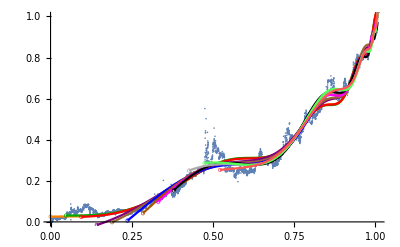

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0473934,0.0947867,0.14218,0.189573,0.236967,0.28436,0.331754,0.379147,0.42654,0.473934,0.521327}

{0.00131681,0.00137714,0.00141903,0.00133322,0.00127348,0.00117641,0.00116561,0.00121634,0.00129542,0.00131433,0.00137742,0.000955102}

{6.66043,6.63645,6.49914,5.78886,5.22508,4.54683,4.22652,4.12097,4.07927,3.82602,3.68046,2.32472}

{0.0362664,0.0370868,0.0376453,0.0364881,0.0356597,0.0342723,0.0341129,0.0348453,0.0359577,0.0362164,0.037072,0.0308667}

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

5065

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

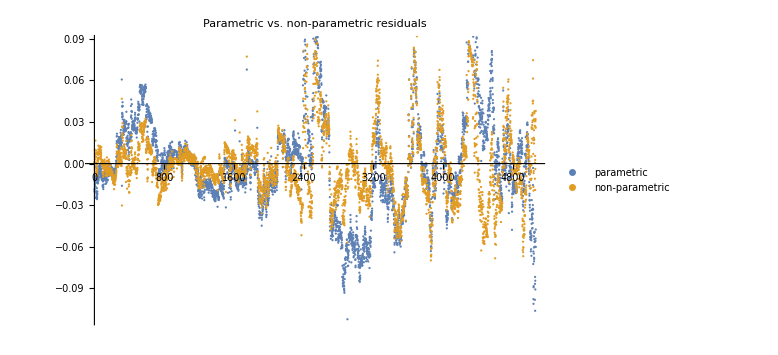

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{3.26058,6.66043}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.0254303,0.0362879}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.000646702,0.00131681}

```mathematica
selN=Length[T1s];
selN
```

12

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{5065,4825,4585,4345,4105,3865,3625,3385,3145,2905,2665,2425}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{5065,4825,4585,4345,4105,3865,3625,3385,3145,2905,2665,2425}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-Silver-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{5065,4825,4585,4345,4105,3865,3625,3385,3145,2905,2665,2425}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.00131681,0.00137714,0.00141903,0.00133322,0.00127348,0.00117641,0.00116561,0.00121634,0.00129542,0.00131433,0.00137742,0.000955102}

```mathematica
RSSs
```

{6.66043,6.63645,6.49914,5.78886,5.22508,4.54683,4.22652,4.12097,4.07927,3.82602,3.68046,2.32472}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.0253606,0.0259368,0.0265167,0.0269552,0.0275853,0.0283759,0.0292319,0.0301685,0.0310823,0.0320318,0.0324512,0.030056}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.912004,σ→-0.0104014,μ→-0.0000742349},{ρ→0.912142,σ→-0.0106298,μ→-0.0000693608},{ρ→0.914055,σ→-0.0107537,μ→-0.0000793791},{ρ→0.91301,σ→-0.0109948,μ→-0.000132257},{ρ→0.913012,σ→-0.0112516,μ→-0.0000998116},{ρ→0.913201,σ→-0.0115619,μ→-0.00011904},{ρ→0.913289,σ→-0.0119048,μ→-0.0000855305},{ρ→0.914467,σ→-0.0122062,μ→-0.0000908377},{ρ→0.91573,σ→-0.0124867,μ→-0.000105933},{ρ→0.915575,σ→-0.0128793,μ→-0.0000872627},{ρ→0.938348,σ→-0.011216,μ→-0.000028271},{ρ→0.958206,σ→-0.0085966,μ→-0.000141231}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[-0.0000742349,{0.912004},0.000108189],ARProcess[-0.0000693608,{0.912142},0.000112992],ARProcess[-0.0000793791,{0.914055},0.000115643],ARProcess[-0.000132257,{0.91301},0.000120885],ARProcess[-0.0000998116,{0.913012},0.000126598],ARProcess[-0.00011904,{0.913201},0.000133678],ARProcess[-0.0000855305,{0.913289},0.000141725],ARProcess[-0.0000908377,{0.914467},0.000148991],ARProcess[-0.000105933,{0.91573},0.000155917],ARProcess[-0.0000872627,{0.915575},0.000165876],ARProcess[-0.000028271,{0.938348},0.000125798],ARProcess[-0.000141231,{0.958206},0.0000739016]}

{15943.8,15083.9,14280.4,13437.3,12599.6,11758.,10921.7,10114.,9327.97,8524.31,8262.87,8110.04}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

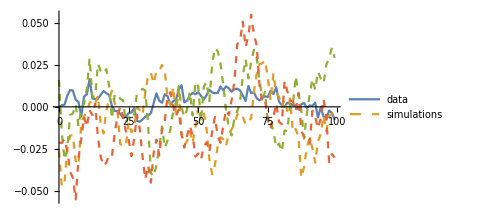
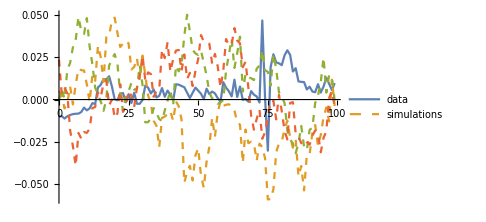
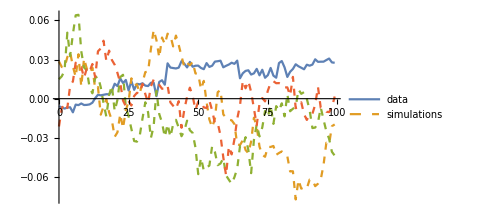
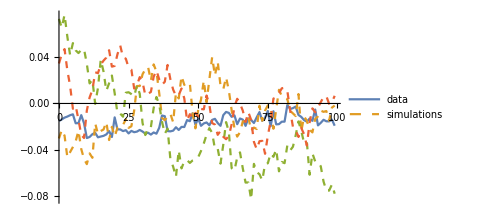
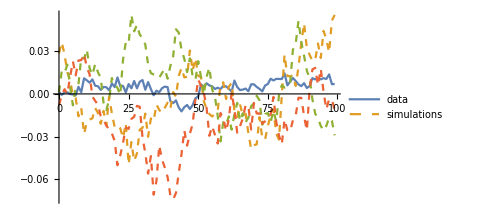
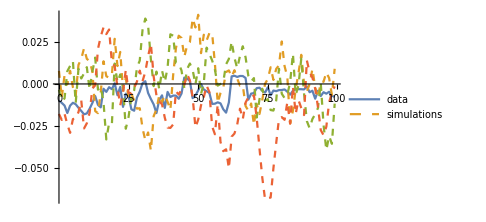
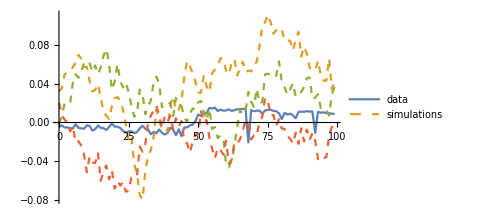
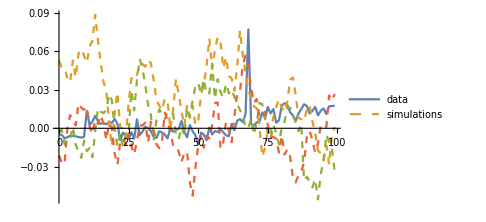

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{17.5819,5041.86},{17.5221,4801.94},{17.54,4561.91},{17.5578,4321.89},{17.58,4081.86},{17.606,3841.83},{17.5267,3601.93},{17.5523,3361.9},{17.5766,3121.87},{17.6109,2881.83},{17.65,2641.78},{17.5368,2401.93}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

5041.86

17.5819

{5041.86,4801.94,4561.91,4321.89,4081.86,3841.83,3601.93,3361.9,3121.87,2881.83,2641.78,2401.93}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 4.78219 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 4.78228 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 709167 Kb

Memory Used: 4.10608 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,0,0,0,0,0,0,0,0,7,12,345}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.007,0.012,0.345}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,True,True,True,True,True,True,False}

```mathematica
(* Take the first / largest interval that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

12

```mathematica
(* As a fallback (if all rejected), take the one with the highest non-zero p-value *)
highestPRejected=ReverseSortBy[Select[MapIndexed[{#1, #2[[1]]}&, selPValues], 0< #[[1]]<(1-0.95)&], {#[[1]],-#[[2]]}&];
highestPRejectedIndex=If[Length[highestPRejected]>0, First[highestPRejected][[2]],{}]
```

11

```mathematica
(* As a fallback (if all rejected, and no positive p-values), take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

1.00626

6

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,If[NumericQ[highestPRejectedIndex], highestPRejectedIndex, minTcIndex]]
```

12

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→1.04133,b→-1.18238,c→-0.066837,d→-0.0833936,T_1→0.521327,tc→1.00626,m→0.5,ω→4.6,RSS→2.32472,ℛerror→0.000955102,ℛσ→0.0308667,LL→8164.82,ρ→0.959289,σ→-0.00871577,μ→-1.8931×10^-17,index→12}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

12

{a→1.04133,b→-1.18238,c→-0.066837,d→-0.0833936,T_1→0.521327,tc→1.00626,m→0.5,ω→4.6,RSS→2.32472,ℛerror→0.000955102,ℛσ→0.0308667,LL→8164.82,ρ→0.959289,σ→-0.00871577,μ→-1.8931×10^-17}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.5

4.6

1.00626

8164.82

```mathematica
t1=Subscript[T, 1]/.fit
```

0.521327

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

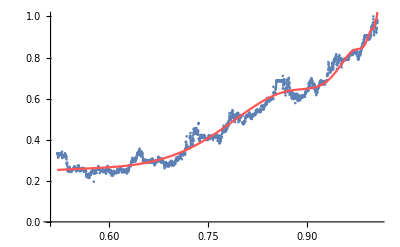

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.04133,b→-1.18238,c→-0.066837,d→-0.0833936,T_1→0.521327,tc→1.00626,m→0.5,ω→4.6,RSS→2.32472,ℛerror→0.000955102,ℛσ→0.0308667,LL→8164.82,ρ→0.959289,σ→-0.00871577,μ→-1.8931×10^-17}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.959289,σ→-0.00871577,μ→-1.8931×10^-17}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

LessEqual::nord: Invalid comparison with 7.11837×10^10-8.70551×10^10 ⅈ attempted.

Less::nord: Invalid comparison with 7.11837×10^10-8.70551×10^10 ⅈ attempted.

LessEqual::nord: Invalid comparison with 7.11837×10^10-8.70551×10^10 ⅈ attempted.

Less::nord: Invalid comparison with 7.11837×10^10-8.70551×10^10 ⅈ attempted.

7.11837×10^10-8.70551×10^10 ⅈ

{1.00526,1.00626}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92005

{1.00526,1.00626,1.00655}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.00616

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Tue 27 Jan 2026 19:28:13

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Wed 28 Jan 2026 00:30:11

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Wed 28 Jan 2026 01:58:02

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Fri 30 Jan 2026 22:04:29

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Tue 3 Feb 2026 23:28:29

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Wed 28 Jan 2026 00:30:11

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Tue 1 Jul 2025 00:00:00 | tc→1.03943 | Tue 3 Feb 2026 23:28:29
T_1→0.0473934 | Thu 10 Jul 2025 22:31:50 | tc→1.03943 | Tue 3 Feb 2026 23:28:29
T_1→0.0947867 | Sun 20 Jul 2025 21:03:41 | tc→1.03943 | Tue 3 Feb 2026 23:28:29
T_1→0.14218 | Wed 30 Jul 2025 19:35:32 | tc→1.03943 | Tue 3 Feb 2026 23:28:29
T_1→0.189573 | Sat 9 Aug 2025 18:07:23 | tc→1.03943 | Tue 3 Feb 2026 23:28:29
T_1→0.236967 | Tue 19 Aug 2025 16:39:14 | tc→1.00626 | Wed 28 Jan 2026 00:30:11
T_1→0.28436 | Fri 29 Aug 2025 15:11:05 | tc→1.00626 | Wed 28 Jan 2026 00:30:11
T_1→0.331754 | Mon 8 Sep 2025 13:42:56 | tc→1.00626 | Wed 28 Jan 2026 00:30:11
T_1→0.379147 | Thu 18 Sep 2025 12:14:47 | tc→1.00626 | Wed 28 Jan 2026 00:30:11
T_1→0.42654 | Sun 28 Sep 2025 10:46:38 | tc→1.00626 | Wed 28 Jan 2026 00:30:11
T_1→0.473934 | Wed 8 Oct 2025 09:18:29 | tc→1.00626 | Wed 28 Jan 2026 00:30:11
T_1→0.521327 | Sat 18 Oct 2025 07:50:19 | tc→1.00626 | Wed 28 Jan 2026 00:30:11

```mathematica
(* Compute price at the low leg of the best Tc: *)
bestP=bestLppls[bestTc-epsilon,bestTc]
```

1.0287

```mathematica
lowCIP=bestLppls[lowCItc,bestTc]
```

1.00289

```mathematica
lastScaledP=bubbleBest[[-1]][[2]]
```

0.982192

```mathematica
lastPriceDate
```

2026-01-31

```mathematica
(* Closing price at `lastPriceDate` date: *)
latestPrice=hourlyPrices[[-1]][[2]]
```

87.897

```mathematica
(* Plot predicted price evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVP[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestPrice/Exp[lastScaledP]]]},{i,min, max,1/8}]
```

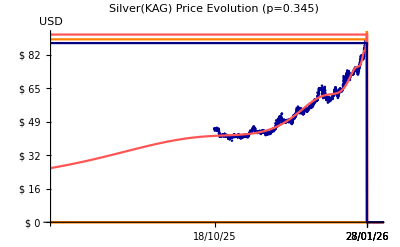

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"Silver(KAG) Price Evolution (p="<>ToString[selPValues[[index]]]<>")",PlotRange->{{0,maxTc},{0,Exp[bestP]}}, Ticks->{ticksH,ticksVP},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestP+1],UnitStep[ti-highCItc]Exp[bestP+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIP],UnitStep[bestTc-ti]Exp[bestP],UnitStep[lastScaledTc-ti]Exp[lastScaledP]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/Silver(KAG)_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/Silver(KAG)_PricePrediction-2026-01-31.png

```mathematica
pToPrice[p_]:= Exp[p] latestPrice/Exp[lastScaledP]
```

```mathematica
(* Check: *)
lastPrice=pToPrice[lastScaledP]
```

87.897

```mathematica
lowCIPrice=pToPrice[lowCIP]
```

89.7352

```mathematica
bestPrice=pToPrice[bestP]
```

92.0816